# Práctica 27 / 09

Tomando apuntes en Mathematica

Pulsando Intro se hacen las operaciones, o también con Shift + Enter.

La función N[Expresion, N.ba de decimales] sirve para dar resultados con decimales, y no de forma exacta.

```mathematica
N[1/3]
```

0.333333

Numero ^ Numero calcula potencias.

```mathematica
23^111
```

14183708525438123863415813843941484832244165610445698528364552777038338914163804399542415764063861458621461135812375854115148666837185816169003740965927

La función Sqrt[Expresion] sirve para dar la raiz cuadrada de un número.

```mathematica
Sqrt[12]
```

2 √3

Todo esto, además de otras cosas como logaritmos, exponenciales, etc. se puede hacer con la paleta, en Palettes.

La función Solve[Expresion, Incógnita] sirve para resolver ecuaciones.

```mathematica
Solve[333x + 1x^2 == 0, x]
```

{{x→-333},{x→0}}

```mathematica
Solve [222x^5 + x^3 + (12x - 5x^2 + 2), x]
```

Solve::naqs: 2 + 12\ x - 5\ x^2 + x^3 + 222\ x^5 is not a quantified system of equations and inequalities.

Solve[2+12 x-5 x^2+x^3+222 x^5,x]

```mathematica
Solve[222x^5 + x^3 + (12x - 5x^2 + 2) == 0, x]
```

{{x→Root[2+12 #1-5 #1^2+#1^3+222 #1^5&,1]},{x→Root[2+12 #1-5 #1^2+#1^3+222 #1^5&,2]},{x→Root[2+12 #1-5 #1^2+#1^3+222 #1^5&,3]},{x→Root[2+12 #1-5 #1^2+#1^3+222 #1^5&,4]},{x→Root[2+12 #1-5 #1^2+#1^3+222 #1^5&,5]}}

```mathematica
a = 2
b = 8

a+ b
```

2

8

10

También pueden usarse variables y operar con ellas, como se ve arriba.

Se pueden utilizar funciones, definiendose de la siguiente forma:

```mathematica
f[x_] := x^2 -3 x
```

```mathematica
f[2]
```

-2

```mathematica
f[x]
```

-3 x+x^2

```mathematica
f[x + x + x - x^2 / 12]
```

-3 (3 x-x^2/12)+(3 x-x^2/12)^2

```mathematica
f''[x]
```

2

```mathematica
f'[x]
```

-3+2 x

```mathematica
f''''''''[x]
```

0

Se puede hacer una lista de elementos de esta forma.

```mathematica
lista1 = {1, 2, 3, 4, 12}
```

{1,2,3,4,12}

```mathematica
2*lista
```

2 lista

```mathematica
2*lista1
```

{2,4,6,8,24}

```mathematica
f[lista1]
```

{-2,-2,0,4,108}

```mathematica
valores = {{-2, f[-2]}, {-1, f[-1]}, {0, f[0], {1, f[1]}}
```

Syntax::bktmcp: Expression "{{-2, f[-2]}, {-1, f[-1]}, {0, f[0], {1, f[1]}}" has no closing ""}"""".

```mathematica
valores = {{-2, f[-2]}, {-1, f[-1]}, {0, f[0]}, {1, f[1]}}
```

{{-2,10},{-1,4},{0,0},{1,-2}}

De la siguiente forma se puede hacer una tabla, con la función Table[]:

```mathematica
TablaValores = Table[{i, f[i]}, {i, -10, 10}]
```

```mathematica
{{-10,130},{-9,108},{-8,88},{-7,70},{-6,54},{-5,40},{-4,28},{-3,18},{-2,10},{-1,4},{0,0},{1,-2},{2,-2},{3,0},{4,4},{5,10},{6,18},{7,28},{8,40},{9,54},{10,70}}

TablaValores = Table[{i, f[i]}, {i, -10, 10, 0.001}]
```

{{-10,130},{-9,108},{-8,88},{-7,70},{-6,54},{-5,40},{-4,28},{-3,18},{-2,10},{-1,4},{0,0},{1,-2},{2,-2},{3,0},{4,4},{5,10},{6,18},{7,28},{8,40},{9,54},{10,70}}

Se puede utilizar ListPlot[lista de valores] para dibujar en un plano los puntos. También se puede usar Plot[funcion, expresion] para dibujar la gráfica. La instrucción Show[dibuja tanto los puntos como la gráfica].

```mathematica
ListPlot[tablaValores]
```

ListPlot::lpn: tablaValores is not a list of numbers or pairs of numbers.

```mathematica
ListPlot[TablaValores]
```

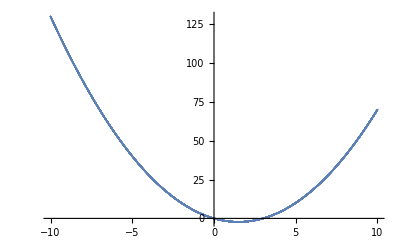
```mathematica
-Graphics-

grafica = Plot[f[x], {x, -12, 4}]
```

-Graphics-

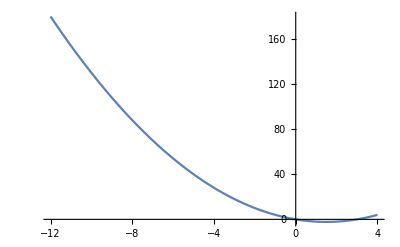

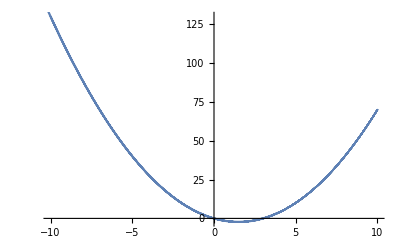

```mathematica
Show[ListPlot[TablaValores], grafica]
```

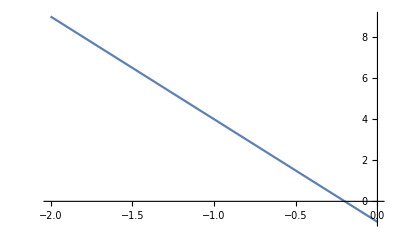

```mathematica
tangente = Plot[f[-1] + f'[-1](x+1), {x, -2, 0}]
```

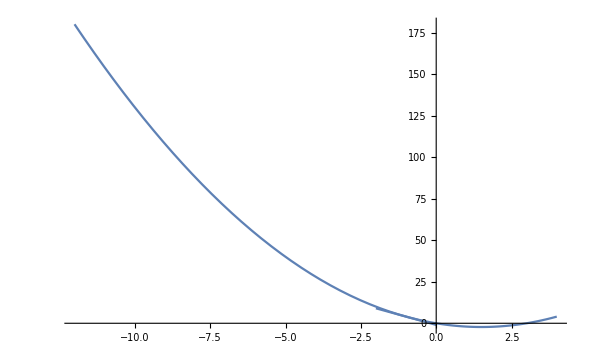

```mathematica
Show[grafica, tangente]
```

```mathematica
∫f[x]ⅆx
```

-(3 x^2)/2+x^3/3

```mathematica
∫_-12^6 f[x]ⅆx
```

810

```mathematica
g[x_, y_] := Sin[x^2 + y^2]
```

```mathematica
Plot3D[g[x, y], {x, -3, 3}, {y, -3, 3}]
```

-Graphics3D-

```mathematica
h[x_] := x^2
```